## Lib + Model Inits

### FCM Lib Import

```mathematica
SetDirectory@NotebookDirectory[]
Needs["FCMLib`",FileNameJoin[{"../lib","FCMLib-cur.wl"}]]
$FCMLibVersion
```

/Users/oosoba/Documents/RAND/Coding/fcm-fusion/socsim

Fuzzy Cognitive Map Library ver. 0.0.8

## Illustrations

### Notes+Snips

```mathematica
(* FCM excerpted from clotting fcm *)
(*{1,"HCP","Hypercoagulation Positional Factors"},
{2,"stas", "Blood Stasis"},
{3,"inju", "Endothelial Injury"},
{4,"HCF", "Hypercoagulation Factors"}*)
(*gspec={{1,2,1},{1,3,-1},{1,4,1},{2,4,-1},{3,1,-1},{3,4,-1},{3,2,1},{4,3,1}};
altGspec={{1,2,1},{1,4,1},{2,4,1},{3,1,-1},{3,2,1},{4,3,1}};
gspec={{1,1,1},{1,2,0.4},{1,3,1}, {1,4,1},{2,3,0.5},{3,2,0.4},{3,4,0.75}};
altGspec={{1,1,1},{1,2,0.4},{1,3,1},{2,3,0.5},{3,2,0.4}};*)
```

### FCM Combination Demo

```mathematica
nds = {
{1,"C1"},
{2,"C2"},
{3,"C3"},
{4,"C4"}
};
nds⟦;;,2⟧ = Map[Style[#, 22,Bold]&, nds⟦;;,2⟧];

gspec1={{1,1,1},{1,2,1},{1,3,1}, {1,4,1},{2,3,1},{3,2,1},{3,4,1}};
gspec2={{1,1,1},{1,2,1},{1,3,1},{2,3,1},{3,2,1}};
gspec3={{1,2,1},{1,4,1},{2,4,1},{3,1,1}, {4,3,1}};
```

```mathematica
expFCMs = {
Graph[FCM[nds,gspec1,0.5],EdgeShapeFunction->GraphElementData["HalfFilledArrow","ArrowSize"->0.1]],
Graph[FCM[nds,gspec2,0.7], EdgeShapeFunction->GraphElementData["HalfFilledArrow","ArrowSize"->0.1]],
Graph[FCM[nds,gspec3,0.5],EdgeShapeFunction->GraphElementData["HalfFilledArrow","ArrowSize"->0.1]]
};

combFCM =FCMJoin[nds,expFCMs,{2,1,1}];
votedFCM=FCMJoinByVote[nds,expFCMs,{2,1,1}];
compfcms = Flatten@{
expFCMs, 
Graph[combFCM,VertexSize->0.4,EdgeShapeFunction->GraphElementData["HalfFilledArrow","ArrowSize"->0.1], ImageSize->72×5], 
Graph[votedFCM,VertexSize->0.5, EdgeShapeFunction->GraphElementData["HalfFilledArrow","ArrowSize"->0.1], ImageSize->72×5]
};
```

```mathematica
compfcms//Dimensions
```

{5}

```mathematica
FCMat/@compfcms⟦;;3⟧
```

{{{1,1,1,1},{0,0,1,0},{0,1,0,1},{0,0,0,0}},{{1,1,1,0},{0,0,1,0},{0,1,0,0},{0,0,0,0}},{{0,1,0,1},{0,0,0,1},{1,0,0,0},{0,0,1,0}}}

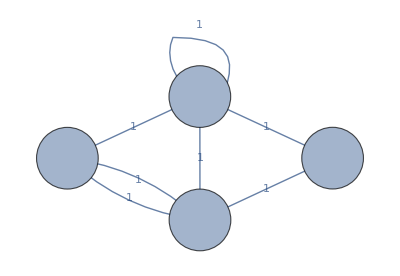
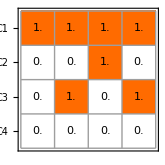
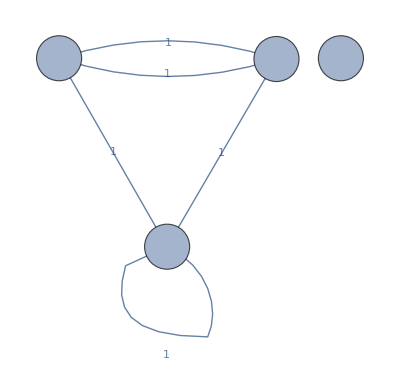
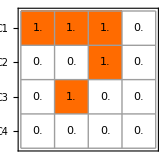
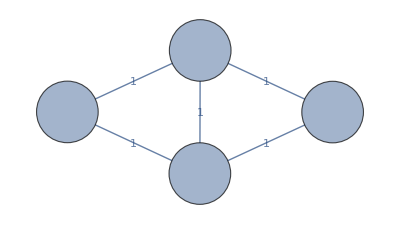
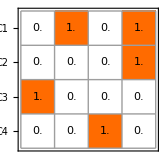
Expert #1 | -Graphics- | -Graphics-
Expert #2 | -Graphics- | -Graphics-
Expert #3 | -Graphics- | -Graphics-

fcm-exps.png

```mathematica
expsfig = Grid[
Transpose@{
Panel/@(Style[#,16]&/@{"Expert #1", "Expert #2", "Expert #3"}),
compfcms⟦;;3⟧,
Panel/@(Show[annotatedMatrixPlot[#], ImageSize->72×2.3]&/@(FCMat/@compfcms⟦;;3⟧))
},
Spacings->{1,1}
]
(*Export["fcm-exps.eps",expsfig]*)
Export["fcm-exps.png",expsfig]
```

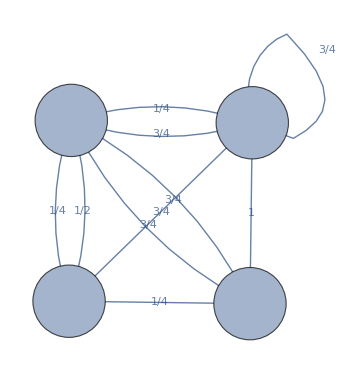
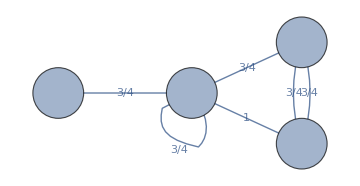
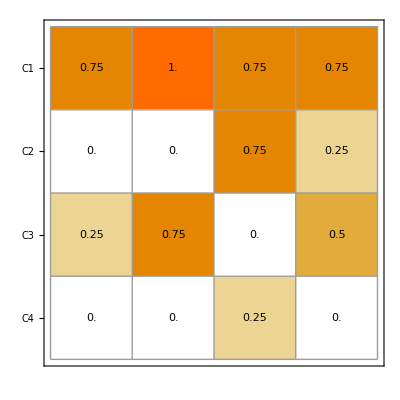
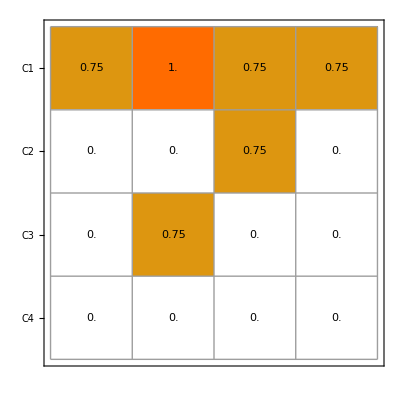
Aggregation by Averaging | Aggregation by Weighted Voting
-Graphics- | -Graphics-
-Graphics- | -Graphics-

fcm-aggs.png

```mathematica
aggsfig=Grid[{
Panel/@(Style[#,16]&/@{"Aggregation by Averaging", "Aggregation by Weighted Voting"}),
compfcms⟦-2;;⟧,
Panel/@(annotatedMatrixPlot/@{FCMat@combFCM,FCMat@votedFCM})
},
Spacings->0
]
(*Export["fcm-aggs.eps",aggsfig]*)
Export["fcm-aggs.png",aggsfig]
```

```mathematica
Directory[]
```

/Users/oosoba/Documents/RAND/Coding/fcm-fusion/socsim

### Step - by - Step Voting - Dev

```mathematica
FCMJoinByVote[nodespec_?MatrixQ,fcms_List,wgts_:0,sz_Real:0.25, asz_Real:0.02]:=Module[
	{n=Length@fcms,ws,fincm,newedgs,ucands,candedgs=(EdgeList/@fcms),votes,vetoedLnks},
	ws = If[
		n==Length@wgts,
		(wgts/Total[wgts]),
		ConstantArray[1/n,n]
	];
	ucands = Sort@Union@Flatten@candedgs;
	votes=Outer[
		Boole@Not@FreeQ[candedgs[[#2]],#1]&,
		ucands, 
		Range@Length@candedgs
		]; (*candedgs is __List*)
	vetoedLnks = ucands[[Select[Range@Length@ucands, (Total[Transpose@votes][[#]]<Ceiling[n/2])&]]];
	fincm = Table[
		EdgeDelete[ f,Intersection[EdgeList[f], vetoedLnks] ], 
		{f,fcms}
	];
	fincm = FCMJoin[nodespec,fincm,ws];
	Return[fincm];
]
```

```mathematica
votedFCM=FCMJoinByVote[nds,expFCMs,{2,1,1}];
```